```mathematica
kD = RandomVariate[NormalDistribution[100,10],50000];
nDs = Table[RandomVariate[NormalDistribution[n,n 0.1],50000],{n,{10,40,80}}];
nkDs = Table[n/kD,{n,nDs}];
```

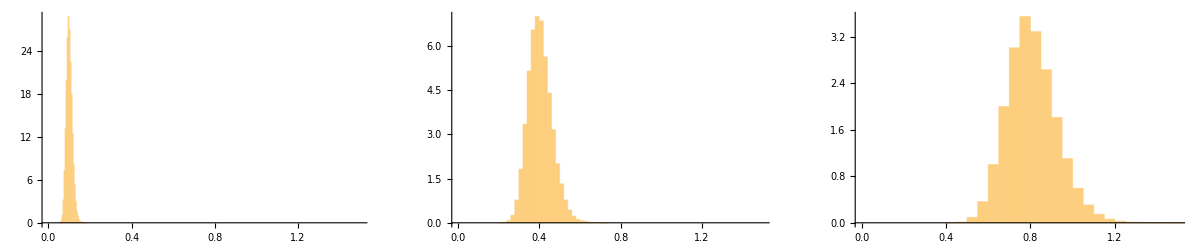

```mathematica
GraphicsRow[Table[Histogram[n,Automatic,"PDF",PlotRange->{{0,1.5},Automatic}]
,{n,nkDs}],ImageSize->Full]
```

```mathematica
ColorData[45,"ColorList"]
```

{RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498]}

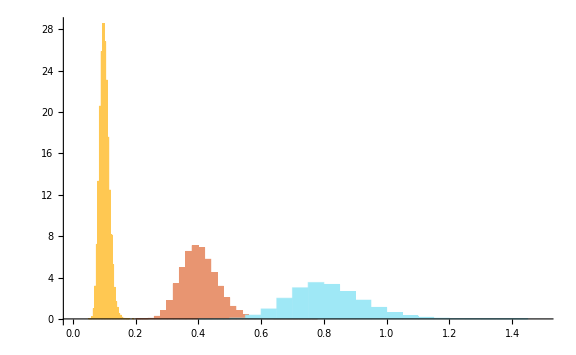

```mathematica
styles={LightYellow, Blue, Gray};
Show[Table[Histogram[nkDs⟦n⟧,Automatic,"PDF",PlotRange->{{0,1.5},Automatic}, ChartStyle->ColorData[45,"ColorList"]⟦5+n⟧]
,{n,{1, 2, 3}}],ImageSize->Large]
```

```mathematica
skd= SmoothKernelDistribution/@ nkDs;
```

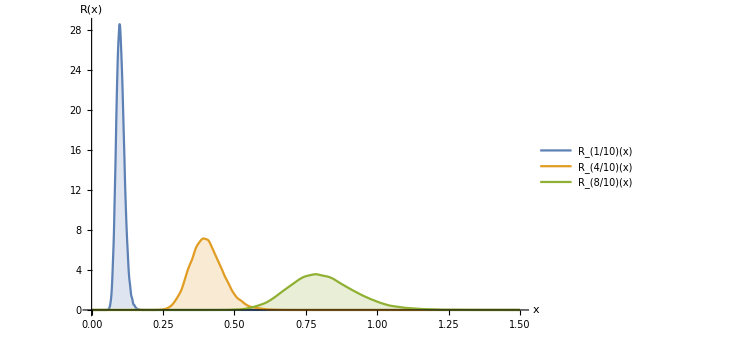

```mathematica
plotRs=Plot[Evaluate[Table[PDF[f,x],{f,skd}]],{x,0,1.5},PlotRange->All,Filling->Bottom,
PlotLegends->Placed[{"R_(1/10)(x)","R_(4/10)(x)","R_(8/10)(x)"},{Right,Center}],AxesLabel->{Style["x",14],Style["R(x)",14]}]
```

```mathematica
SetDirectory["/Users/franciszekrakowski/cognitive/kwantyfikatory"]
```

/Users/franciszekrakowski/cognitive/kwantyfikatory

```mathematica
Export["plotRs.eps",plotRs, ImageResolution->200]
```

plotRs.eps

## Numeric reactive units visualisation.

```mathematica
xList=Table[x,{x,0,150,0.01}];
ruNumeric=ParallelTable[Table[PDF[NormalDistribution[n,1],x],{x,xList}]/.x_/;x<0.0001->0,{n,1,100}];
```

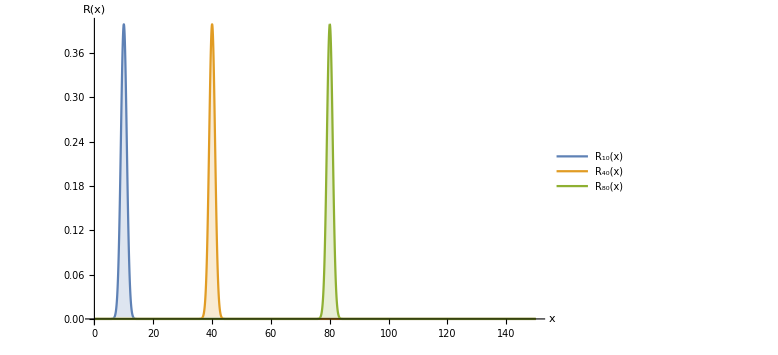

```mathematica
ListLinePlot[Table[{xList,ruNumeric⟦k⟧}//Transpose, {k, {10,40, 80}}],PlotRange->All,ImageSize->Large, Filling->Bottom,PlotLegends->Placed[{"R_10(x)","R_40(x)","R_80(x)"},{Right,Center}],AxesLabel->{Style["x",14],Style["R(x)",14]}]
```

## Works with Darek 17.01.2022

### Precise

#### Numeric reactive units visualisation sigma = 0.3

```mathematica
xList=Table[x,{x,0,150,0.01}];
ruNumeric=ParallelTable[Table[PDF[NormalDistribution[n,0.3],x],{x,xList}]/.x_/;x<0.0001->0,{n,1,10}];
```

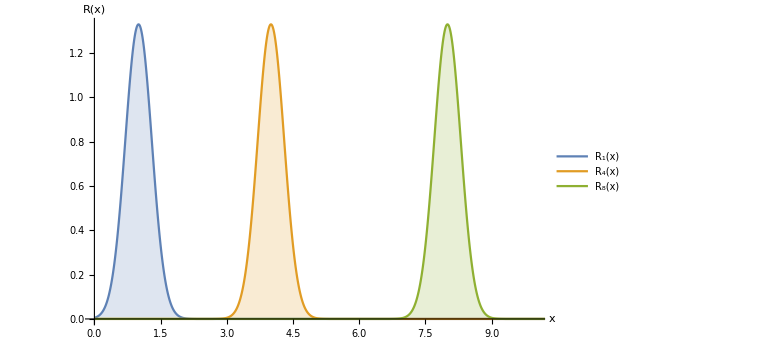

```mathematica
preciseNumericSigma03=ListLinePlot[Table[{xList,ruNumeric⟦k⟧}//Transpose, {k, {1,4, 8}}],PlotRange->{{0,10},All},ImageSize->Large, Filling->Bottom,PlotLegends->Placed[{"R_1(x)","R_4(x)","R_8(x)"},{Right,Center}],AxesLabel->{Style["x",14],Style["R(x)",14]}]
```

#### Quotient reactive units visualisation -sigma = 0.3

```mathematica
kD = RandomVariate[NormalDistribution[100,0.3],50000];
nDs = Table[RandomVariate[NormalDistribution[n,0.3],50000],{n,{10,40,80}}];
nkDs = Table[n/kD,{n,nDs}];
```

```mathematica
skd= SmoothKernelDistribution/@ nkDs;
```

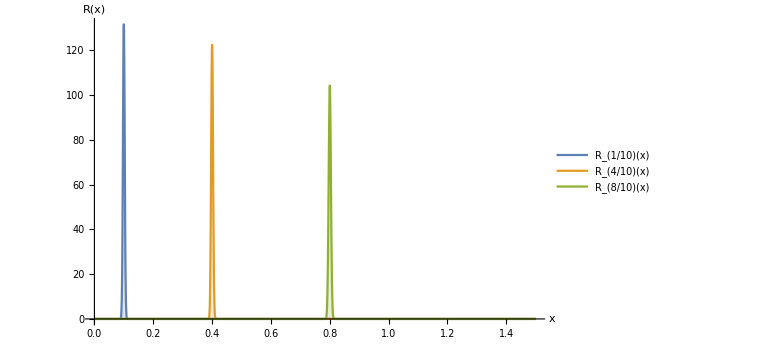

```mathematica
preciseQuotientSigma03=Plot[Evaluate[Table[PDF[f,x],{f,skd}]],{x,0,1.5},PlotRange->All,Filling->Bottom,
PlotLegends->Placed[{"R_(1/10)(x)","R_(4/10)(x)","R_(8/10)(x)"},{Right,Center}],AxesLabel->{Style["x",14],Style["R(x)",14]},ImageSize->Large]
```

```mathematica
SetDirectory["/Users/franciszekrakowski/cognitive/kwantyfikatory/results_UNIFORM/17.01.2022"]
```

/Users/franciszekrakowski/cognitive/kwantyfikatory/results_UNIFORM/17.01.2022

```mathematica
Export["preciseNumericSigma03.eps",preciseNumericSigma03, ImageResolution->200];
Export["preciseQuotientSigma03.eps",preciseQuotientSigma03, ImageResolution->200];
```

### Vague

#### Numeric reactive units visualisation sigma = 1

```mathematica
xList=Table[x,{x,0,150,0.01}];
ruNumeric=ParallelTable[Table[PDF[NormalDistribution[n,1],x],{x,xList}]/.x_/;x<0.0001->0,{n,1,10}];
```

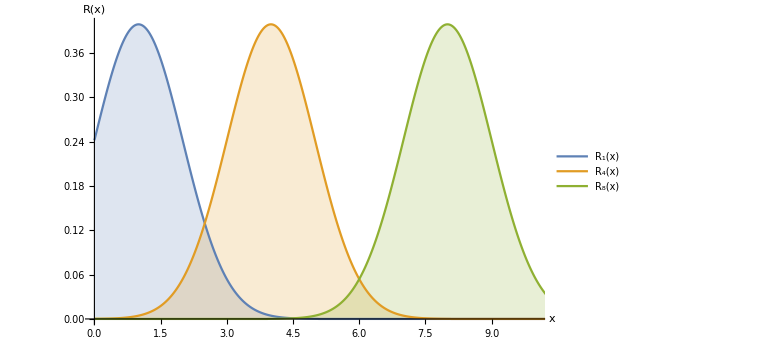

```mathematica
vagueNumericSigma1=ListLinePlot[Table[{xList,ruNumeric⟦k⟧}//Transpose, {k, {1,4, 8}}],PlotRange->{{0,10},All},ImageSize->Large, Filling->Bottom,PlotLegends->Placed[{"R_1(x)","R_4(x)","R_8(x)"},{0.95,0.8}],AxesLabel->{Style["x",14],Style["R(x)",14]}]
```

#### Quotient reactive units visualisation -sigma = 1

```mathematica
kD = RandomVariate[NormalDistribution[100,1],50000];
nDs = Table[RandomVariate[NormalDistribution[n,1],50000],{n,{10,40,80}}];
nkDs = Table[n/kD,{n,nDs}];
```

```mathematica
skd= SmoothKernelDistribution/@ nkDs;
```

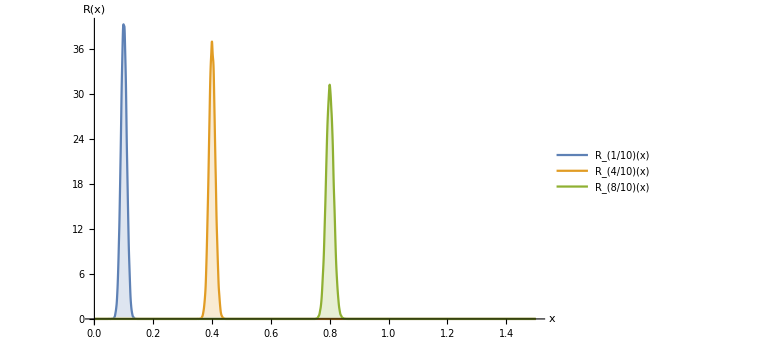

```mathematica
vagueQuotientSigma1=Plot[Evaluate[Table[PDF[f,x],{f,skd}]],{x,0,1.5},PlotRange->All,Filling->Bottom,
PlotLegends->Placed[{"R_(1/10)(x)","R_(4/10)(x)","R_(8/10)(x)"},{Right,Center}],AxesLabel->{Style["x",14],Style["R(x)",14]},ImageSize->Large]
```

```mathematica
SetDirectory["/Users/franciszekrakowski/cognitive/kwantyfikatory/results_UNIFORM/17.01.2022"]
```

/Users/franciszekrakowski/cognitive/kwantyfikatory/results_UNIFORM/17.01.2022

```mathematica
Export["vagueNumericSigma1.eps",preciseNumericSigma1, ImageResolution->200];
Export["vagueQuotientSigma1.eps",preciseQuotientSigma1, ImageResolution->200];
```